# ModeCode Mockup

## Basics building blocks

#### Choose the number of fields and Npivot

```mathematica
d=2;
Npivot=55;
Mpc2Mpl=2.6245*^-57;
Nsubhorizon=10;
```

#### Fields, mometa, modes

[JF] Might want to make ψαβ and παβ symmetric combinations (if that makes sense!) for speed purpouses

```mathematica
ϕα = Table[Symbol["ϕ" <> ToString[i]][t], {i, d}];
pα = Table[Symbol["p" <> ToString[i]][t], {i, d}];

ψαβ = Table[Symbol["ψ" <> ToString[i]<>ToString[j]][t], {i, d}, {j, d}];
παβ = Table[Symbol["π" <> ToString[i]<>ToString[j]][t], {i, d}, {j, d}];
Print["ψαβ = ",ψαβ//MatrixForm," ", "παβ = ",παβ//MatrixForm ]
```

ψαβ = (ψ11[t] | ψ12[t]
ψ21[t] | ψ22[t]) παβ = (π11[t] | π12[t]
π21[t] | π22[t])

```mathematica
ϕparameters = Table[Symbol["ϕ" <> ToString[i]], {i, d}];
pparameters = Table[Symbol["p" <> ToString[i]], {i, d}];
ψparameters=Flatten[ Table[Symbol["ψ" <> ToString[i]<>ToString[j]], {i, d}, {j, d}]];
πparameters = Flatten[Table[Symbol["π" <> ToString[i]<>ToString[j]], {i, d}, {j, d}]];

backgroundparameters=Join[ϕparameters,pparameters];
allparameters=Join[backgroundparameters,ψparameters,πparameters]
```

{ϕ1,ϕ2,p1,p2,ψ11,ψ12,ψ21,ψ22,π11,π12,π21,π22}

### Potentials and background initial conditions

#### Double quadratic

```mathematica
ϕIC={10.31001803105938,12.93651907528955};
(*M=10^-5;
mϕ=1M;
mχ=9M;*)
mϕ=√(10^-10.422895047377294);
mχ=√(10^(-10.422895047377294+Log10[81.0]));
W=1/2 mϕ^2 ϕ1[t]^2+1/2 mχ^2 ϕ2[t]^2;
```

### Background quantities

```mathematica
H=Sqrt[W/(3-ϵ)];

ϵ=1/2 pα.pα;

ϵSR=1/2(Wα.Wα)/W^2;
HSR=Sqrt[W/3];
Wα=Map[D[W,#]&,ϕα];
Wαβ=Outer[D[#1,#2]&,Wα,ϕα];
```

### Other stuff the code needs

[JF] Need “DifferentialEquations`InterpolatingFunctionAnatomy`” for extracting Nend from NDSolve.

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"]
```

[JF] This stuff is for making the plots a little less ugly.

```mathematica
Labels=Directive[Darker[Blue],FontFamily->"Helvetica Neue",FontSize->12];
ThickBlue=Directive[Thick,Blue];
ThickRed=Directive[Thick,Red];
ThickOrange=Directive[Thick,Orange];
ThickGreen=Directive[Thick,Green];
ThickPurple=Directive[Thick,Purple];
ThickYellow=Directive[Thick,Darker[Yellow,0.2]];
ThickDarkRed=Directive[Thick,Blend[{Red,Blue},0.15]];
```

## Solve for the background to get ICs for the mode eqations

### Prepare background equations for solver

#### Initial conditions (N.B this uses SLOW-ROLL ICs)

[JF] N.B this uses slow-roll initial conditions

```mathematica
ϕinitialsub=Thread[Rule[ϕα,ϕIC]];
ϕinitial=Thread[(ϕα/.t->0)==ϕIC]
pIC=First[-Wα/W/.{ϕinitialsub}];
(*pIC={0,0};*)
pinitial=Thread[(pα/.t->0)==pIC]
```

{ϕ1[0]==10.31,ϕ2[0]==12.9365}

{p1[0]==-0.00150931,p2[0]==-0.153398}

#### Background (Klein--Gordon split up for a bit of excitement)

[JF] N.B this use of mapping is not your usual way. UPDATE: changed it now but it is actually very slightly slower using a list of equations rather than the vector structure you had
[JF] This splitting seems to be slower than using the second order equation....Maybe you should check this, and try to understand why.

```mathematica
KG=Join[Table[D[ϕα[[i]], t]==pα[[i]],{i,d}],Table[D[pα[[i]], t]==-(3-ϵ)pα[[i]]-(3-ϵ)Wα[[i]]/W,{i,d}]];
(*KG//MatrixForm*)
```

```mathematica
tmin=0;
tmax=10000;
allbackgroundequations=Join[KG,ϕinitial,pinitial];
```

### Solve!

[JF] Solve Klein--Gordon equation, stopping when ϵ = 1. Stopping the solver when ϵ=1 massively speeds things up. Thanks Layne!

```mathematica
Timing[backgroundsol=NDSolve[allbackgroundequations,backgroundparameters,{t,tmin,tmax},MaxSteps->∞,Method->{"EventLocator","Event"->{ϵ-1}}]]
```

{0.03631,{{ϕ1→InterpolatingFunction[{{0.,69.6815}},<>],ϕ2→InterpolatingFunction[{{0.,69.6815}},<>],p1→InterpolatingFunction[{{0.,69.6815}},<>],p2→InterpolatingFunction[{{0.,69.6815}},<>]}}}

```mathematica
Nend = InterpolatingFunctionDomain[First[ϕ1/. backgroundsol]][[1,-1]];
Print["N_end= ",Nend]
```

N_end= 69.6815

## Output from background solution

### Background plots

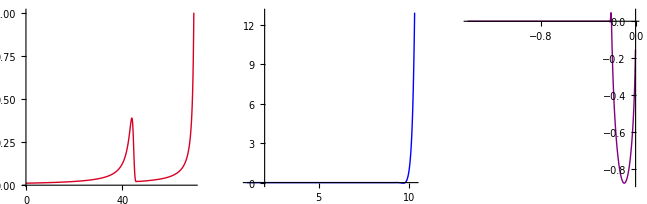

```mathematica
GraphicsRow[{
Plot[Re[ϵ]/.backgroundsol,{t,0,Nend},
PlotStyle->ThickDarkRed,PlotRange->All],

ParametricPlot[ϕα/.backgroundsol,{t,0,Nend},PlotStyle->ThickBlue,PlotRange->All],

ParametricPlot[pα/.backgroundsol,{t,0,Nend},PlotStyle->ThickPurple,PlotRange->All]
}]
```

### Useful quantities

```mathematica
Print["N_(exit temp)"]
Nexittemp=Nend-Npivot
Print["H_exit"]
Hexit=First[H/.backgroundsol/.t->Nexittemp]
Print["ϵ_exit"]
ϵexit=First[ϵ/.backgroundsol/.t->Nexittemp]
Print["ϕ_α^exit"]
ϕexit=First[ϕα/.backgroundsol/.t->Nexittemp]
```

N_(exit temp)

14.6815

H_exit

0.000238336

ϵ_exit

0.0176413

ϕ_α^exit

{10.2832,10.462}

## Solve for the perturbations

[JF] You can’t start with Bunch--Davies initital conditions at the beginning of inflation. See Pesky & Schroeder. Instead, they should start say 5 or 10 e-folds before horizon exit.

### Quantities obtained from background solution - NB YOU MUST CHOOSE THE CONVENTION

[JF] Define N_BD to be the time associated with Bunch--Davies initial conditions.
[JF] Choose option 1 or option 2 and comment out the rest (Maybe turn this into an if statement and set it at the top of the code)

#### OPTION 1: Set k using k=a*H* and start with Bunch--Davies ICs at Nsubhorizon e-folds prior to Nexit = 0.

[JF] There are actaully a bunch of slightly different implemtations here. They all seem to work (as well as they should) now as best as I can tell.

```mathematica
(*Print["N_(BD temp)"]
NBDtemp=Nexittemp-Nsubhorizon
Print["H_BD"]
HBD=First[H/.backgroundsol/.t->NBDtemp]
Print["ϵ_BD"]
ϵBD=First[ϵ/.backgroundsol/.t->NBDtemp]
Print["ϕ_α^BD"]
ϕBD=First[ϕα/.backgroundsol/.t->NBDtemp]
Print["p_α^BD"]
pBD=First[pα/.backgroundsol/.t->NBDtemp]

Nexit=0;
a0=1;
NBD=Nexit-Nsubhorizon;
k=ⅇ^Nexit Hexit;
aBD=ⅇ^NBD;
Print["k = ", k]
Print["k/a_BD = ", k/(aBD HBD)]
a=a0 ⅇ^t;

If[NBDtemp≤0,
Print["YOU CAN NOT COUNT e-folds CORRECTLY"],
Print["YOUR MODEL LOOKS GOOD!"]
]*)

(*NBD=NBDtemp
Nexit=Nexittemp
k=ⅇ^Nexit Hexit;
aBD=ⅇ^NBD
a=ⅇ^t*)

(*screwing with the normalisation*)
(*NBD=NBDtemp
Nexit=Nexittemp
a0=ⅇ^-Nexit;
a=a0 ⅇ^t
k=a0 ⅇ^Nexit Hexit;
aBD=a/.t->NBD*)

(*NBD=0;
Nexit=Nsubhorizon;
k=ⅇ^Nexit Hexit;
aBD=ⅇ^NBD
a=ⅇ^t*)
```

#### OPTION 2: Set a0 using k=a*H*

[JF] This should be the same as Layne’s code and ModeCode

```mathematica
(*Nexit=0;*)
k=.002 Mpc2Mpl;(*Specify in Mpc and converts to Subscript[M, Pl]^-1*)

aexit=k/(Hexit ⅇ^Nexittemp);
atemp=aexit ⅇ^t;

NBDsub=First[FindRoot[{atemp H == k/100}/.backgroundsol,{t,Nexittemp}]];
NBDtemp=t/.NBDsub;

HBD=First[H/.backgroundsol/.t->NBDtemp];
ϵBD=First[ϵ/.backgroundsol/.t->NBDtemp];
ϕBD=First[ϕα/.backgroundsol/.t->NBDtemp];
pBD=First[pα/.backgroundsol/.t->NBDtemp];

NBD=0;
Nexit=Nexittemp-NBDtemp;
a0=k/(Hexit ⅇ^Nexit);
a=a0 ⅇ^t;
aBD=a/.t->NBD;
Print["N_exit = ",Nexit]
Print["N_BD = ",NBD]
Print["a_BD = ",aBD]
Print["H_BD = ", HBD]
Print["ϵ_BD = ", ϵBD]
Print["ϕ_α^BD = ", ϕBD]
Print["p_α^BD = ", pBD]
```

N_exit = 4.6817

N_BD = 0

a_BD = 2.0401×10^-58

H_BD = 0.000257292

ϵ_BD = 0.0151745

ϕ_α^BD = {10.293,11.3083}

p_α^BD = {-0.00194774,-0.174199}

#### Initial conditions

[JF] Confused about these initial conditions. Why is e^(ⅈk/aH)=1 ?! On subhorizon scales 1/k<<1/aHso.....wtf!

```mathematica
ψBDstart=Thread[(Flatten[ψαβ]/.t->NBD)==Flatten[IdentityMatrix[d]*1/(√(2k))]];
πBDstart=Thread[(Flatten[παβ]/.t->NBD)==Flatten[IdentityMatrix[d]*(- ⅈ)/(aBD HBD)√(k/2)]];
(*ψBDstart=Thread[(Flatten[ψαβ]/.t->NBD)==Flatten[IdentityMatrix[d]*1/(√(2k))ⅇ^((ⅈ k)/(aBD HBD))]];
πBDstart=Thread[(Flatten[παβ]/.t->NBD)==Flatten[IdentityMatrix[d]*(- ⅈ)/(aBD HBD)√(k/2)ⅇ^((ⅈ k)/(aBD HBD))]];*)
Print["Possibly require a factor of ",ⅇ^(ⅈ k/(aBD HBD))]
```

Possibly require a factor of 0.862319-0.506366 ⅈ

```mathematica
ϕBDstart=Thread[(ϕα/.t->NBD)==ϕBD];
pBDstart=Thread[(pα/.t->NBD)==pBD];
```

### Equation of motion for the modes

#### Mass Matrix

```mathematica
Cαβ=Table[Wαβ[[i,j]]/H^2+1/H^2(pα[[i]]Wα[[j]]+Wα[[i]]pα[[j]])+(3-ϵ)pα[[i]]pα[[j]],{i,d},{j,d}];
(*Cαβ//MatrixForm*)
```

#### Equation of motion (split again for no good reason)

```mathematica
ψEq=Flatten[Table[D[ψαβ[[i,j]], t]==παβ[[i,j]],{i,d},{j,d}]];
πEq=Flatten[Table[D[παβ[[i,j]], t]==-(1-ϵ)παβ[[i,j]]-(k^2/(a^2 H^2)-2+ϵ)ψαβ[[i,j]]-Sum[Cαβ[[i,l]]ψαβ[[l,j]],{l,d}],{i,d},{j,d}]];
(*ψEq//MatrixForm
πEq//MatrixForm*)
```

```mathematica
allequations=Join[KG,ψEq,πEq,ϕBDstart,pBDstart,ψBDstart,πBDstart];
```

### Solve for everything!!!

[JF] Full solution includes background equations and mode equations. Not sure if this is the best way to do it but stick with it for now.

```mathematica
Timing[fullsol=NDSolve[allequations,allparameters,{t,NBD,Nexit+Npivot}(*,Method->"BDF"*),AccuracyGoal->20,MaxSteps->∞]]
```

{0.24709,{{ϕ1→InterpolatingFunction[{{0.,59.6817}},<>],ϕ2→InterpolatingFunction[{{0.,59.6817}},<>],p1→InterpolatingFunction[{{0.,59.6817}},<>],p2→InterpolatingFunction[{{0.,59.6817}},<>],ψ11→InterpolatingFunction[{{0.,59.6817}},<>],ψ12→InterpolatingFunction[{{0.,59.6817}},<>],ψ21→InterpolatingFunction[{{0.,59.6817}},<>],ψ22→InterpolatingFunction[{{0.,59.6817}},<>],π11→InterpolatingFunction[{{0.,59.6817}},<>],π12→InterpolatingFunction[{{0.,59.6817}},<>],π21→InterpolatingFunction[{{0.,59.6817}},<>],π22→InterpolatingFunction[{{0.,59.6817}},<>]}}}

## Output from full solution

[JF] Check background still looks sensible.

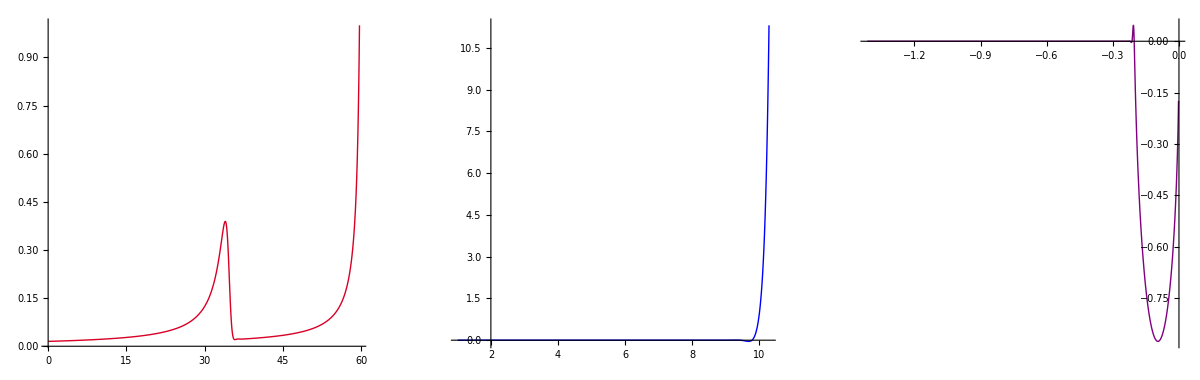

```mathematica
GraphicsRow[{
Plot[Re[ϵ]/.fullsol,{t,NBD,Nexit+Npivot},
PlotStyle->ThickDarkRed,PlotRange->All],

ParametricPlot[Re[ϕα]/.fullsol,{t,NBD,Nexit+Npivot},PlotStyle->ThickBlue,PlotRange->All],

ParametricPlot[Re[pα]/.fullsol,{t,NBD,Nexit+Npivot},PlotStyle->ThickPurple,PlotRange->All]
}]
```

[JF] Check imaginary parts

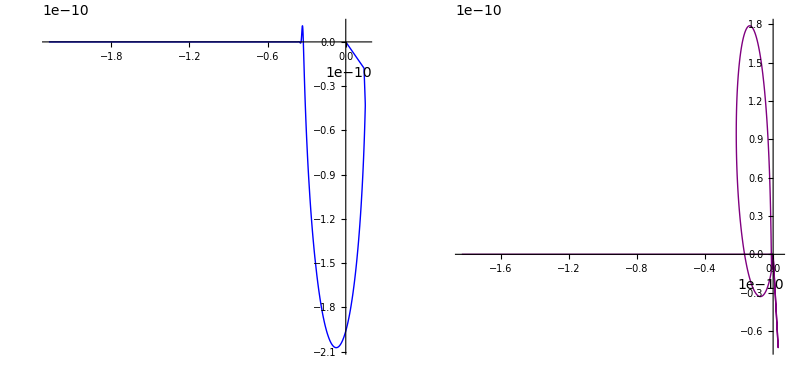

```mathematica
GraphicsRow[{ParametricPlot[Im[ϕα]/.fullsol,{t,NBD,Nexit+Npivot},PlotStyle->ThickBlue,PlotRange->All,AspectRatio->1/GoldenRatio],ParametricPlot[Im[pα]/.fullsol,{t,NBD,Nexit+Npivot},PlotStyle->ThickPurple,PlotRange->All]}]
```

```mathematica
(*GraphicsRow[{Plot[Re[k/(a H)]/.fullsol,{t,NBD,Nexit+Npivot},
PlotStyle->ThickDarkRed,PlotRange->All],Plot[Re[k/(a H)]/.fullsol,{t,Nexit,Npivot},
PlotStyle->ThickDarkRed,PlotRange->All]}]
GraphicsRow[{Plot[Im[k/(a H)]/.fullsol,{t,NBD,Nexit+Npivot},
PlotStyle->ThickDarkRed,PlotRange->All],Plot[Im[k/(a H)]/.fullsol,{t,Nexit,Npivot},
PlotStyle->ThickDarkRed,PlotRange->All]}]*)
```

[JF] The real part of the modes plotted twice. Once just for the subhorizon evolutoin, once just for the superhorizon evolution.

```mathematica
GraphicsGrid[{{
Plot[Re[ψ11[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[Re[ψ12[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickBlue,PlotRange->All],
Plot[Re[ψ21[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickPurple,PlotRange->All],
Plot[Re[ψ22[t]]/.fullsol,{t,NBD,Nexit},PlotStyle->ThickOrange,PlotRange->All]
},{
Plot[Re[ψ11[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[Re[ψ12[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickBlue,PlotRange->All],
Plot[Re[ψ21[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickPurple,PlotRange->All],
Plot[Re[ψ22[t]]/.fullsol,{t,Nexit,Npivot},PlotStyle->ThickOrange,PlotRange->All]
}}]
```

-Graphics-

## Observables

### Powerspectrum

```mathematica
Pαβ=k^3/(2 π^2)Table[Sum[ψαβ[[i,l]]/a((ψαβ[[j,l]])*)/a,{l,d}],{i,d},{j,d}];
```

```mathematica
ωζ=pα/(√(2 ϵ));
```

```mathematica
NPζ=Nexit+Npivot;
Pζ=1/(2ϵ)Sum[ωζ[[i]]ωζ[[j]]Pαβ[[i,j]],{i,d},{j,d}];
Print["P_ζ^end = ",First[Evaluate[Pζ/.fullsol/.t->NPζ]]]
```

P_ζ^end = 7.80721×10^-8-2.019×10^-17 ⅈ

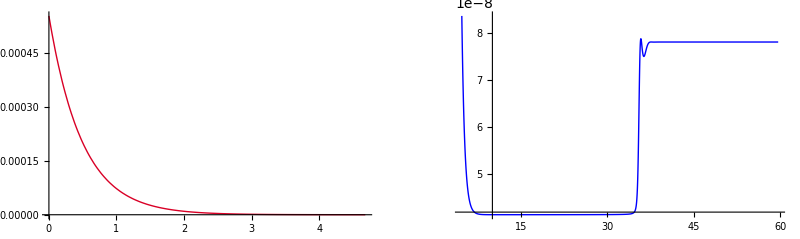

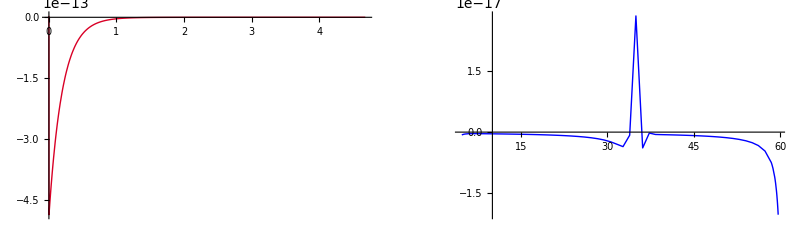

```mathematica
GraphicsRow[{Plot[Re[Pζ]/.fullsol,{t,NBD,Nexit},
PlotStyle->ThickDarkRed,PlotRange->All],
Plot[Re[Pζ]/.fullsol,{t,Nexit,Nexit+Npivot},
PlotStyle->ThickBlue,PlotRange->All]}]
GraphicsRow[{Plot[Im[Pζ]/.fullsol,{t,NBD,Nexit},
PlotStyle->ThickDarkRed,PlotRange->All],
Plot[Im[Pζ]/.fullsol,{t,Nexit,Nexit+Npivot},
PlotStyle->ThickBlue,PlotRange->All]}]
```

[JF] Feild correlation functions...kind of. N.B factors of “a” etc.
[JF] NB time range

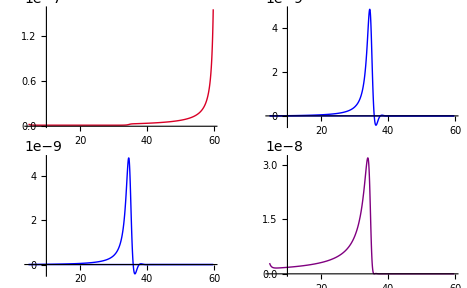

```mathematica
Nplotstart=Nexit;
Nplotend = Nexit+Npivot;

GraphicsGrid[{{
Plot[Pαβ[[1,1]]/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[{Re[Pαβ[[1,2]]],Im[Pαβ[[1,2]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All]
},{
Plot[{Re[Pαβ[[2,1]]],Im[Pαβ[[2,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All],
Plot[Pαβ[[2,2]]/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickPurple,PlotRange->All]
}}]
(*GraphicsGrid[{{
Plot[a^2 Pαβ[[1,1]]/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[{Re[a^2 Pαβ[[1,2]]],Im[Pαβ[[1,2]]]}/.fullsol,{t,Nplotstart,Nplotend},
PlotStyle->{ThickBlue},PlotRange->All]
},{
Plot[{Re[a^2 Pαβ[[2,1]]],Im[Pαβ[[2,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All],
Plot[a^2 Pαβ[[2,2]]/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickPurple,PlotRange->All]
}}]*)
```

[JF] Mass Matrix C_αβ

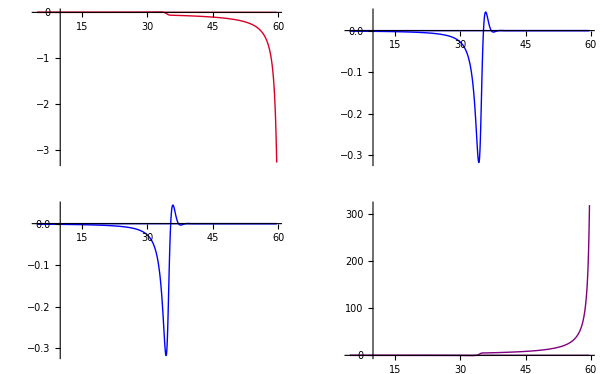

```mathematica
GraphicsGrid[{{
Plot[{Re[Cαβ[[1,1]]],Im[Cαβ[[1,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[{Re[Cαβ[[1,2]]],Im[Cαβ[[1,2]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All]
},{
Plot[{Re[Cαβ[[2,1]]],Im[Cαβ[[2,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All],
Plot[{Re[Cαβ[[2,2]]],Im[Cαβ[[2,2]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickPurple,PlotRange->All]
}}]
```

## Comparison with ModeCode

```mathematica
SetDirectory["~/Documents/ModeCode_multifield"];
```

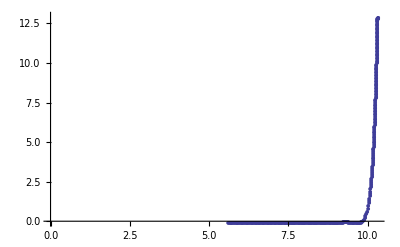

```mathematica
MCtrajectorydata=Import["phiarr.txt","Table"];
MCtrajectoryN=MCtrajectorydata[[All,1]];
MCtrajectoryϕ1=MCtrajectorydata[[All,2]];
MCtrajectoryϕ2=MCtrajectorydata[[All,3]];
plotfrommodecode=ListPlot[Thread[{MCtrajectoryϕ1,MCtrajectoryϕ2}],PlotMarkers->{Automatic,5}]
```

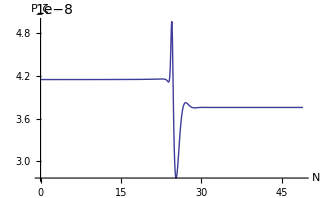

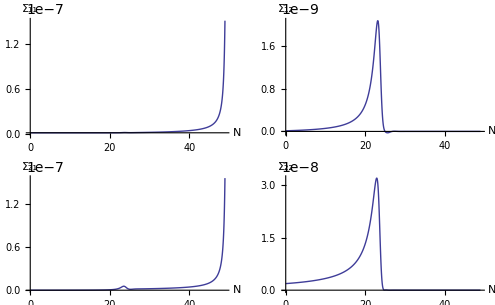

```mathematica
MCPζdata=Import["pow.txt","Table"];
MCPζN=MCPζdata[[All,1]];
MCPζ=MCPζdata[[All,2]];
ListPlot[Thread[{MCPζN-MCPζN[[1]],MCPζ}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","P_ζ"}]

MCPϕϕdata=Import["powmatrix.txt","Table"];
MCPϕϕN=MCPϕϕdata[[All,1]];
MCP11=MCPϕϕdata[[All,2]];
MCP12=MCPϕϕdata[[All,3]];
MCP21=MCPϕϕdata[[All,4]];
MCP22=MCPϕϕdata[[All,5]];
GraphicsGrid[{{
ListPlot[Thread[{MCPζN-MCPζN[[1]],MCP11}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","Σ_11"}],
ListPlot[Thread[{MCPζN-MCPζN[[1]],MCP12}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","Σ_12"}]},{
ListPlot[Thread[{MCPζN-MCPζN[[1]],MCP21}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","Σ_21"}],
ListPlot[Thread[{MCPζN-MCPζN[[1]],MCP22}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","Σ_22"}]
}}]
```

## Debugging with Layne

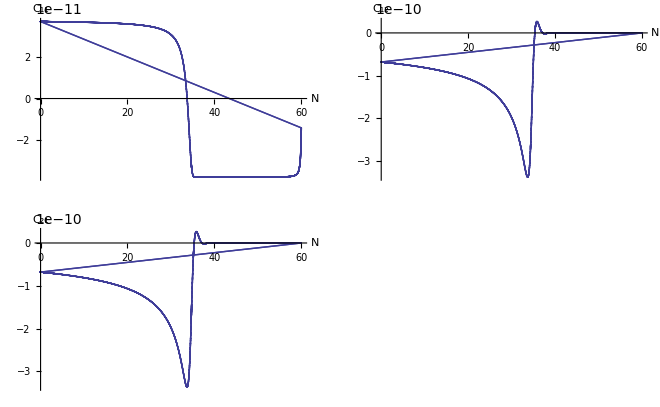

```mathematica
MCCdata=Import["fort.314","Table"];
MCCN=MCCdata[[All,1]];
MCC11=MCCdata[[All,2]];
MCC12=MCCdata[[All,3]];
MCC21=MCCdata[[All,4]];
MCC22=MCCdata[[All,5]];
GraphicsGrid[{{
ListPlot[Thread[{MCCN-MCCN[[1]],MCC11}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","C_11"}],
ListPlot[Thread[{MCCN-MCCN[[1]],MCC12}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","C_12"}]},{
ListPlot[Thread[{MCCN-MCCN[[1]],MCC21}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","C_21"}],
ListPlot[Thread[{MCCN-MCCN[[1]],MCC22}](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","C_22"}]
}}]
```

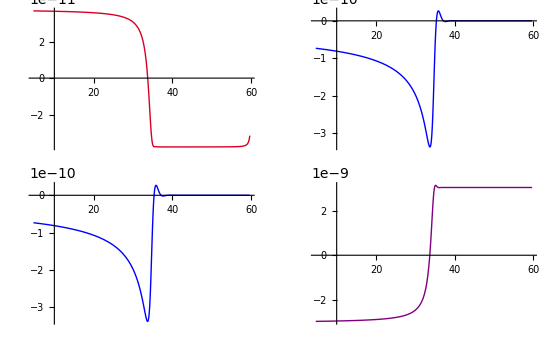

```mathematica
GraphicsGrid[{{
Plot[{Re[H^2 Cαβ[[1,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[{Re[H^2 Cαβ[[1,2]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All]
},{
Plot[{Re[H^2 Cαβ[[2,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All],
Plot[{Re[H^2 Cαβ[[2,2]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickPurple,PlotRange->All]
}}]
```

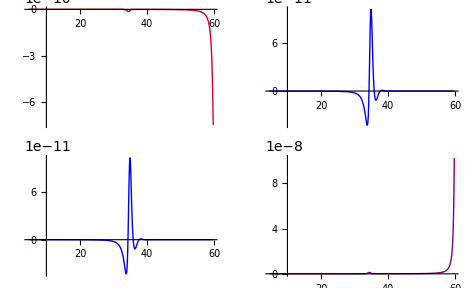

```mathematica
GraphicsGrid[{{
Plot[{Im[Cαβ[[1,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickDarkRed,PlotRange->All],
Plot[{Im[Cαβ[[1,2]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All]
},{
Plot[{Im[Cαβ[[2,1]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->{ThickBlue},PlotRange->All],
Plot[{Im[Cαβ[[2,2]]]}/.fullsol,{t,Nplotstart,Nplotend},PlotStyle->ThickPurple,PlotRange->All]
}}]
```

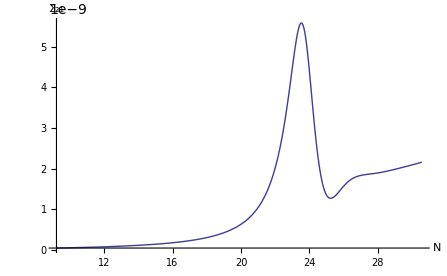

```mathematica
ListPlot[Thread[{MCPζN-MCPζN[[1]],MCP21}][[200;;700]](*,PlotMarkers->{Automatic,5}*),Joined->True,PlotRange->All,AxesLabel->{"N","Σ_21"}]
```